# Node 124 research

## Read network 2

```mathematica
root = "~/research/posecpp/";
```

```mathematica
rdata=ReadList[root<>"/geo/geostd_with_mean.txt",{Number,Number,Real,Real,Real,Real,Real,Real}];
```

```mathematica
Length[rdata]
```

483216

```mathematica
rgood=Select[rdata,#[[2]]>100&];
```

```mathematica
rgood[[All,5]]=Sqrt[rgood[[All,5]]]/Abs[rgood[[All,8]]];
```

```mathematica
rselected=Select[rgood,Total[#[[3;;5]]]<1.5&&Quotient[#[[1]],10000]≠Mod[#[[1]],10000]&];rgraph=Graph[Map[Quotient[#[[1]],10000]<->Mod[#[[1]],10000]&,rselected]];
```

```mathematica
VertexCount[rgraph]
EdgeCount[rgraph]
```

645

4368

```mathematica
Mean[rgood[[All,8]]]
```

1.09468

```mathematica
Mean[rselected[[All,8]]]
```

0.859731

```mathematica
NeighborhoodGraph[rgraph,596,VertexLabels->"Name"]
```

-Graphics-

## Check self consistency by self co-occurrences

```mathematica
goodHeadList = ReadList["~/git/posecpp/res/head_clusters_trimmed_2.txt"];badList={124,392,818,585,542,113};
```

```mathematica
selfNodes=Select[rgood,Quotient[#[[1]],10000]==Mod[#[[1]],10000]&];
selfHeadNodes = Select[selfNodes,MemberQ[goodHeadList,Quotient[#[[1]],10000]]&];
selfBadNodes = Select[selfNodes,MemberQ[badList,Quotient[#[[1]],10000]]&];
```

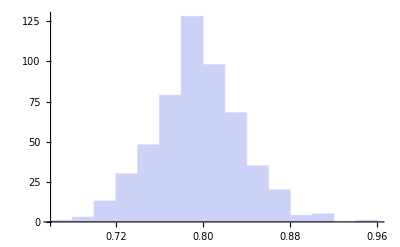
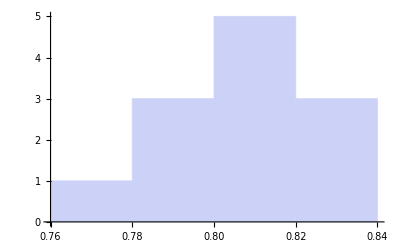
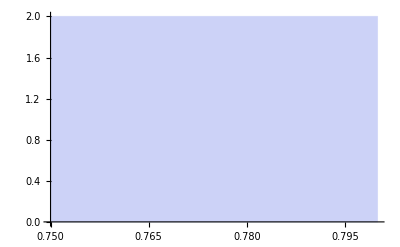

```mathematica
{Histogram[selfNodes[[All,8]]],Histogram[selfHeadNodes[[All,8]]],Histogram[selfBadNodes[[All,8]]]}
```

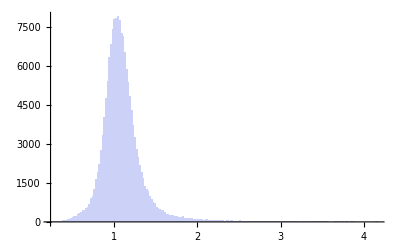

```mathematica
Histogram[rgood[[All,8]]]
```